# Równania różniczkowe zwyczajne

## Zagadnienie: znajdź funkcję x(t)

dx/dt= F(x,t)
x(t_0)=x_0

## Metoda naiwna

dx/dt=(x(t + h) - x(t))/h= F(x,t) =>x(t + h) =x(t)+ h F(x,t)

## Szereg Taylora na ratunek

Przypomnienie: wzór Taylora: x(t+h) = ∑_(n=0)^∞ 1/(n!)x^(n)(t)h^n
Znając wartość funkcji x w czasie t, możemy wyznaczyć jej wartość w punkcie t+h, jeśli znamy pochodne F(x,t)

Dla problemu: dx/dt=F(x,t), x(t_0)=x_0 znamy pierwszą pochodną!

Metoda Eulera: tylko wyraz liniowy w h: x(t+h)=x(t)+x'(t)h=x(t)+F(x,t)h

Metoda Eulera wyższego rzędu:
x(t+h)=x(t)+F(x,t)h+1/2 F'(x,t) h^2+1/6 F''(x,t)h^3

## Metoda Euler’a

Przykład: Rozwiąż równanie metodą Eulera (liniową): dx/dt= x(t), x(t=0)=x_0= 2, h=10^-2
x(t + h) = x(t) + x(t)h

```mathematica
Clear[x]
sol=DSolveValue[{x'[t]==x[t],x[0]==2},x,t]
```

Function[{t},2 ⅇ^t]

1/1000

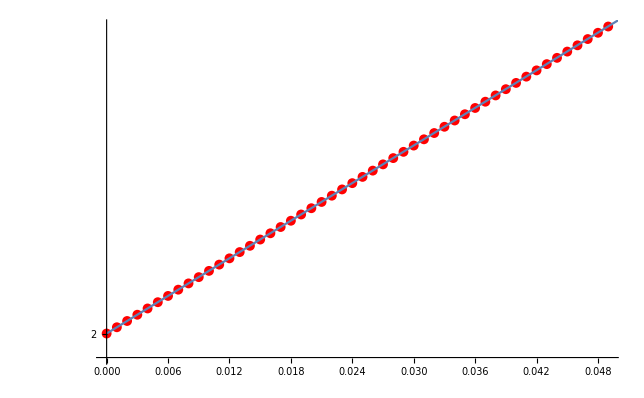

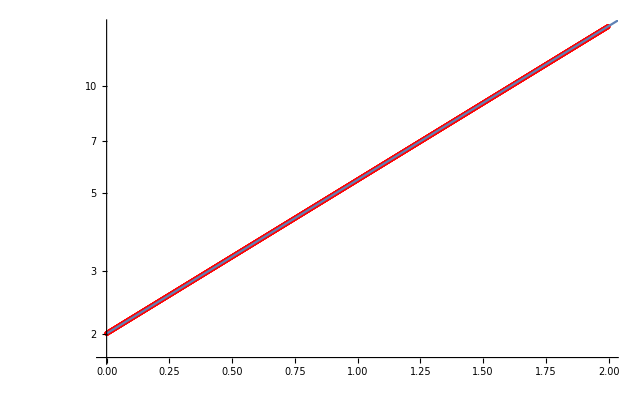

```mathematica
x={{0,2}};
h=10^-3
For[i=2,i<2000,i++,
AppendTo[x, {N[x[[i-1,1]]+h],N[x[[i-1,2]]+x[[i-1,2]]h]}]
]
Show[{
ListLogPlot[x[[;;50]],PlotStyle->Red],
LogPlot[{sol[t]},{t,0,2}]}]
Show[{
ListLogPlot[x,PlotStyle->Red],
LogPlot[{sol[t]},{t,0,20}]}]
```

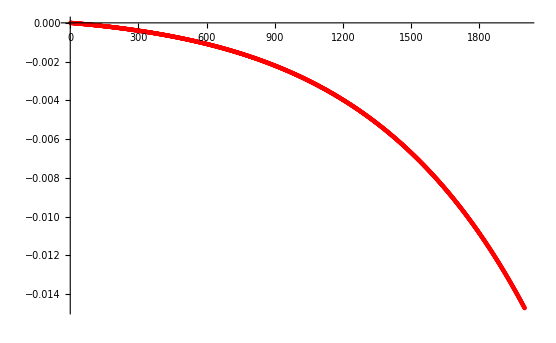

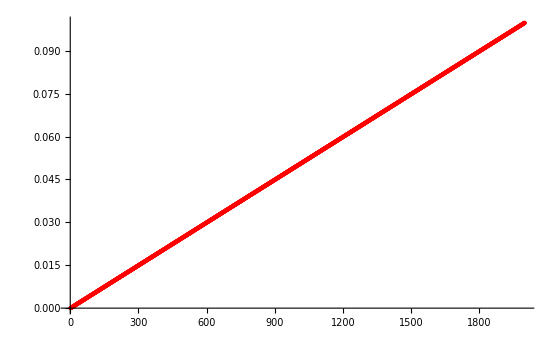

```mathematica
exact=Table[{t0,N@sol[t0]},{t0,0,x[[-1,1]]+h,h}];
Show[{
ListPlot[(x[[All,2]]-exact[[All,2]]),PlotStyle->Red]}]
Show[{
ListPlot[Abs[(x[[All,2]]-exact[[All,2]])/exact[[All,2]]]*100,PlotStyle->Red]}]
```

Metoda wyższego rzędu:
x(t+h)=x(t)+x(t)h+x(t)h^2/2+x(t)h^3/6

1/100

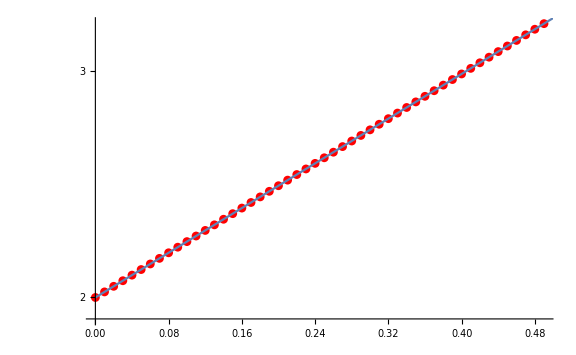

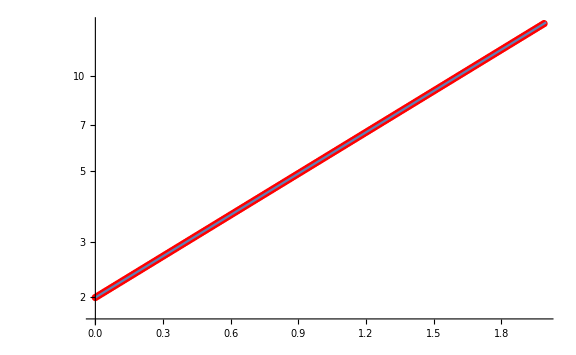

```mathematica
x={{0,2}};
h=10^-2
For[i=2,i<2000,i++,
AppendTo[x, {
N[x[[i-1,1]]+h],
N[x[[i-1,2]]+x[[i-1,2]]h+1/2 x[[i-1,2]] h^2+1/6 x[[i-1,2]] h^3]}]
]
Show[{
ListLogPlot[x[[;;50]],PlotStyle->Red],
LogPlot[{sol[t]},{t,0,2}]},ImageSize->Large]
Show[{
ListLogPlot[x[[;;200]],PlotStyle->Red],
LogPlot[{sol[t]},{t,0,2}]},ImageSize->Large]
```

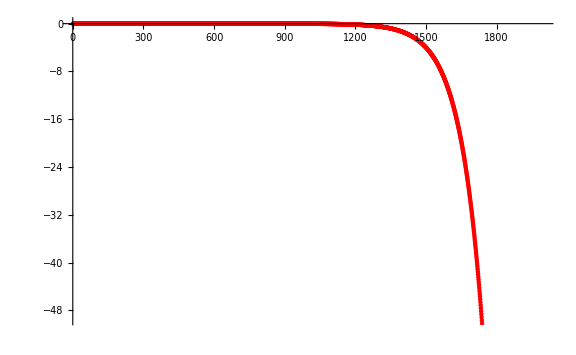

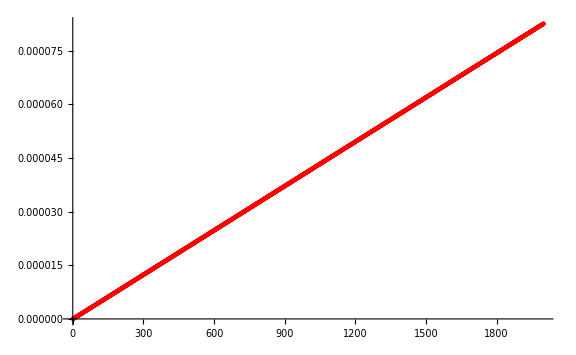

```mathematica
exact=Table[{t0,N@sol[t0]},{t0,0,x[[-1,1]],h}];
Show[{
ListPlot[(x[[All,2]]-exact[[All,2]]),PlotStyle->Red]},ImageSize->Large]
Show[{
ListPlot[Abs[(x[[All,2]]-exact[[All,2]])/exact[[All,2]]]*100,PlotStyle->Red]},ImageSize->Large]
```

Przykład: Rozwiąż równanie metodą Eulera (liniową): dx/dt= x(t)*cos(x(t)), x(t=0)=x_0= 1
x(t + h) = x(t) + x(t)cos(x(t))h

```mathematica
Simplify[D[y[t]Cos[y[t]],t]/.{y'[t]-> y[t]Cos[y[t]]}]
```

Cos[y[t]] y[t] (Cos[y[t]]-Sin[y[t]] y[t])

1/100

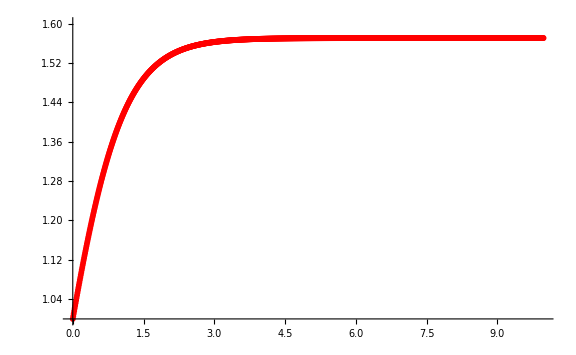

```mathematica
x={{0,1}};
h=10^-2
For[i=2,i<1000,i++,
AppendTo[x, {
N[x[[i-1,1]]+h],
N[x[[i-1,2]]+x[[i-1,2]]*Cos[x[[i-1,2]]]h]}]
]

Show[{
ListPlot[x,PlotStyle->Red,PlotRange->{1,1.6}]
},ImageSize->Large]
```

{{y→InterpolatingFunction[…]}}

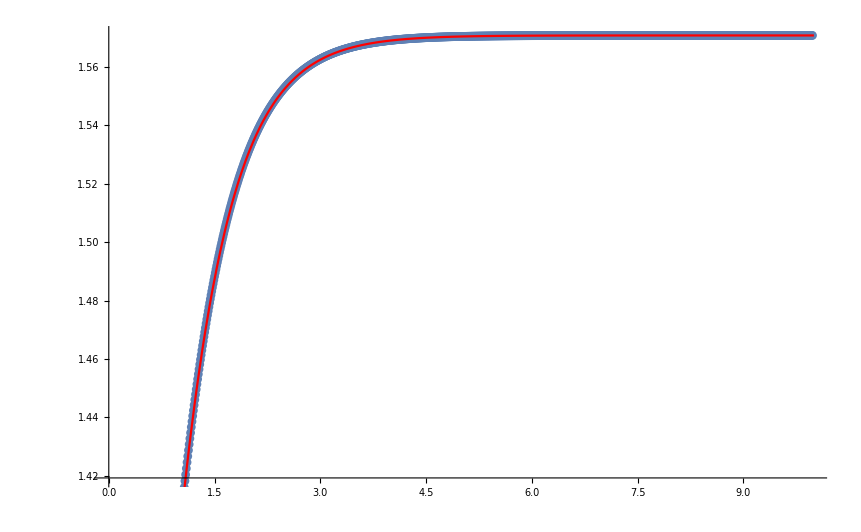

```mathematica
sol=NDSolve[{y'[t]==y[t]Cos[y[t]],y[0]==1},y,{t,0,10}]
Show[{
ListPlot[x],
Plot[{y[t]/.sol},{t,0,10},PlotRange->All,PlotLegends->"Expressions",PlotStyle->Red]
}]
```

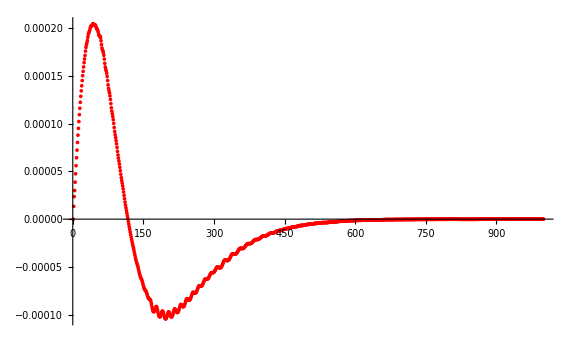

```mathematica
exact=Table[{t0,N[y[t0]/.sol][[1]]},{t0,0,x[[-1,1]]+h,h}];

Show[{
ListPlot[(x[[All,2]]-exact[[All,2]])/exact[[All,2]]*100,PlotStyle->Red,PlotRange->All]},ImageSize->Large]
```

```mathematica
Simplify[D[f[t]*Cos[f[t]],t]/.{f'[t]->f[t]Cos[f[t]]}]
```

Cos[f[t]] f[t] (Cos[f[t]]-f[t] Sin[f[t]])

```mathematica
Length[x]
Length[exact]
```

1000

1999

1/100

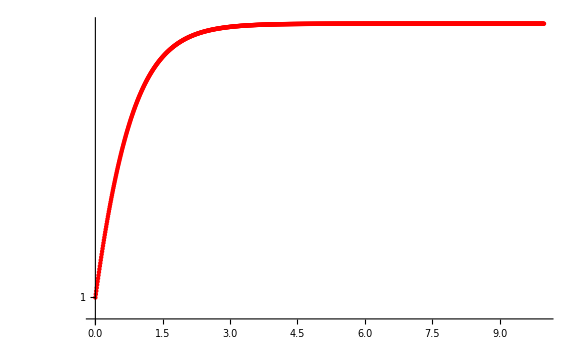

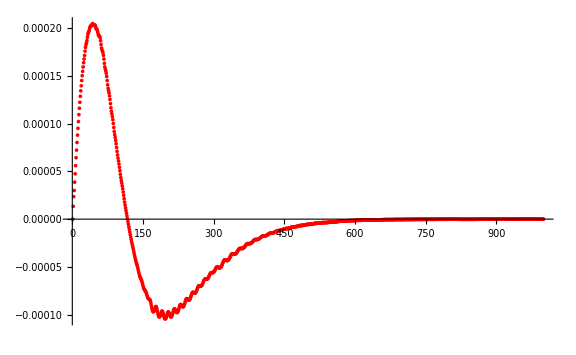

```mathematica
x={{0,1}};
h=10^-2
For[i=2,i<=1000,i++,
AppendTo[x, {
N[x[[i-1,1]]+h],
N[x[[i-1,2]]+x[[i-1,2]]*Cos[x[[i-1,2]]]h+h^2/2 x[[i-1,2]]*Cos[x[[i-1,2]]](Cos[x[[i-1,2]]]-x[[i-1,2]]*Sin[x[[i-1,2]]])]}];
]

Show[{
ListLogPlot[x,PlotStyle->Red]
},ImageSize->Large]
Show[{
ListPlot[(x[[All,2]]-exact[[All,2]])/exact[[All,2]]*100,PlotStyle->Red]},ImageSize->Large,PlotRange->All]
```

## Równania różniczkowe drugiego rzędu

### Problem: Rozwiąż równanie oscylatora: (d^2 x)/dt^2 + b dx/dt+c x=0

```mathematica
Clear[x]
sol=DSolveValue[x''[t]+b x'[t]+c x[t]==0,x,t]
```

Function[{t},ⅇ^(1/2 (-b-√(b^2-4 c)) t) C[1]+ⅇ^(1/2 (-b+√(b^2-4 c)) t) C[2]]

### Jak zastosować metodę Eulera? Wprowadzamy nową zmienną dx/dt=v(t)

dv/dt + b v(t)+c x(t)=0
dx/dt = v(t)

dv/dt =- b v(t)-c x(t)
dx/dt = v(t)

v(t+Δt)=v(t)-( b v(t)+c x(t)) Δt
x(t+Δt) =x(t)+ v(t) Δt

### Przykład 1: x(0) = 1, v(0) = 0, b = 0.75, c = 4

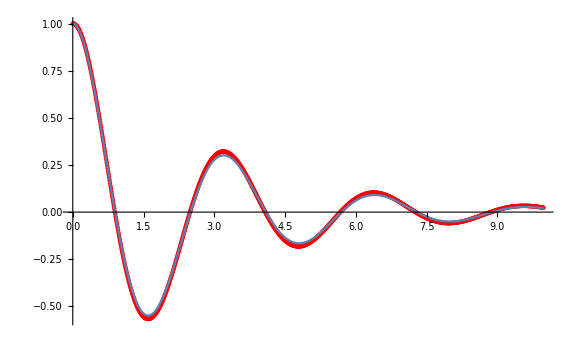

```mathematica
x={{0,1}};
v={{0,0}};
h=10^-2;
b=0.75;
c=4;
g[t_]:= ⅇ^(-0.375 t) ( Cos[1.964529205687714 t]+0.1908854288927333 Sin[1.964529205687714 t])
For[i=2,i<1000,i++,
AppendTo[v, {
N[v[[i-1,1]]+h],
N[v[[i-1,2]]-(b v[[i-1,2]]+c x[[i-1,2]])h]}];
AppendTo[x, {
N[x[[i-1,1]]+h],
N[x[[i-1,2]]+v[[i-1,2]]*h]}]

]

Show[{
ListPlot[x,PlotStyle->Red,PlotRange->All],
Plot[g[t],{t,0,10},PlotRange->All]
},ImageSize->Large]
```

```mathematica
DSolveValue[{y''[t]+b y'[t]+c y[t]==0,y[0]==1,y'[0]==0},y,t]
```

Function[{t},1. ⅇ^(-0.375 t) (1. Cos[1.96453 t]+0.190885 Sin[1.96453 t])]

### Przykład 2: Wahadło. Rozwiąż równanie wahadła: (d^2 x)/dt^2+ sin(x(t))=0 z warunkami początkowymi x(0) = 1, x’(0) = 0 , a następnie porównaj wynik z przybliżeniem sin(x)≈x

dv/dt+ sin(x(t))=0
dx/dt= v(t)

v(t+Δt)=v(t) - sin(x(t)) Δt
x(t+Δt) =x(t) + v(t) Δt

0.1

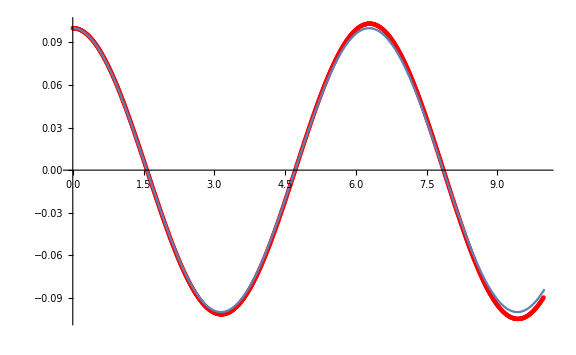

```mathematica
x0=0.1
x={{0,x0}};
v={{0,0}};
h=10^-2;
For[i=2,i<1000,i++,
AppendTo[v, {
N[v[[i-1,1]]+h],
N[v[[i-1,2]]-Sin[ x[[i-1,2]]]h]}];
AppendTo[x, {
N[x[[i-1,1]]+h],
N[x[[i-1,2]]+v[[i-1,2]]*h]}]

]

Show[{
ListPlot[x,PlotStyle->Red,PlotRange->All],
Plot[ x0 Cos[t],{t,0,10},PlotRange->All]
},ImageSize->Large]
```

```mathematica
DSolve[{y''[t]+y[t]==0,y[0]==1,y'[0]==0},y,t]
```

{{y→Function[{t},Cos[t]]}}

Metoda Eulera może powodować niestabilności!

## Leap-frog

(d^2 x)/dt^2= A(x(t))

Najpierw obliczamy prędkość w połowie kroku: v(t+Δt/2)=v(t-Δt/2)+A(x(t))Δt  ,
i korzystamy z niej aby obliczyć położenie:
x(t+Δt)=x(t)+v(t+Δt/2)Δt

```mathematica
Import["C:\\work\\programowanie\\PiMN2024\\wyklad\\ODE\\leapfrog.png"]
```

-Graphics-

Co jeśli nasze warunki początkowe to:
x(t_0) = x_0, v(t_0)=v_0? Do metody leapfrog potrzebujemy v w połowie kroku (Δt):
v(t+1/2 Δt)=v(t)+1/2 Δt A(x)

Przykład: x’’(t) = x(t), x(0) = 1, x’(0) = 0 - rozwiązanie analityczne to x(t)=cosh(t)

Function[{t},1/2 ⅇ^-t (1+ⅇ^(2 t))]

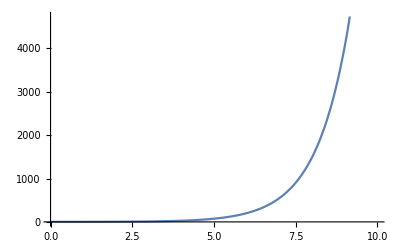

```mathematica
sol=DSolveValue[{y''[t]==y[t],y[0]==1,y'[0]==0},y,t]
Plot[sol[t],{t,0,10}]
```

Równanie x’’(t)=x(t), możemy zapisać w następujący sposób: v’(t)=x(t), v(t) = x’(t)

1/200

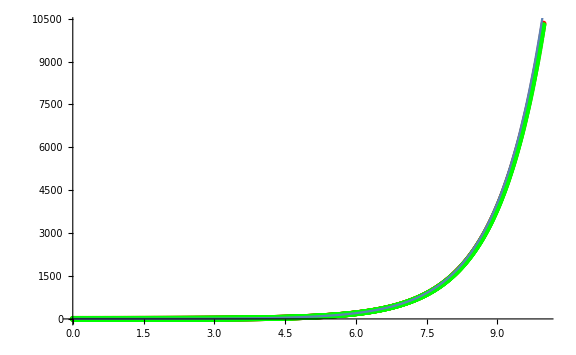

```mathematica
x0=1;
x1={{0,1}};
h=10^-2;

v12=1/2 h*( x0)
vl={{0,v12}};

Clear[i]
For[i=2,i<1000,i++,
AppendTo[vl, {
N[vl[[i-1,1]]+h],
N[vl[[i-1,2]]+( x1[[i-1,2]])h]}];
AppendTo[x1, {
N[x1[[i-1,1]]+h],
N[x1[[i-1,2]]+vl[[i-1,2]]*h]}]

]
x={{0,1}};
v={{0,0}};
h=10^-2;

For[i=2,i<1000,i++,
AppendTo[v, {
N[v[[i-1,1]]+h],
N[v[[i-1,2]]+( x[[i-1,2]])h]}];
AppendTo[x, {
N[x[[i-1,1]]+h],
N[x[[i-1,2]]+v[[i-1,2]]*h]}]

]
Show[{
ListPlot[x1,PlotStyle->Red,PlotRange->All],
ListPlot[x,PlotStyle->Green,PlotRange->All],
Plot[ Cosh[t],{t,0,10},PlotRange->All]
},ImageSize->Large]
```

Błędy względne:

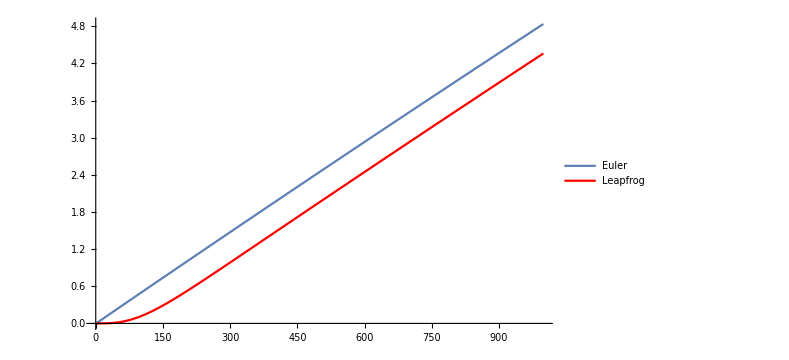

```mathematica
Show[{
ListPlot[Abs[(x[[All,2]]-Cosh[x[[All,1]]])/Cosh[x[[All,1]]]]*100,Joined->True,PlotLegends->{"Euler"}],
ListPlot[Abs[(x1[[All,2]]-Cosh[x1[[All,1]]])/Cosh[x1[[All,1]]]]*100,Joined->True,PlotStyle->Red,PlotLegends->{"Leapfrog"}]
}]
```

## Metody Verlet’a

### Równanie: x’’(t) = A(x), x(t_0) = x_0, x'(t_0)=v_0, x_n=x(t_n),t_n=t_0+nΔt

x_1= x_0+v_0 Δt+1/2 A(x_0)Δt^2
x_(n+1)=2 x_n-x_(n-1)+A(x_n)Δt^2
Uwaga! Powyższy zapis działa też dla wektorów

Problem dwóch ciał:
x1’’(t) =-x1/((x1^2+y1^2)^(3/2)) ,
y1’’(t) =-y1/((x1^2+y1^2)^(3/2)) ,

5

0

{0.5}

1/100

{5.,5.}

{0.,0.005}

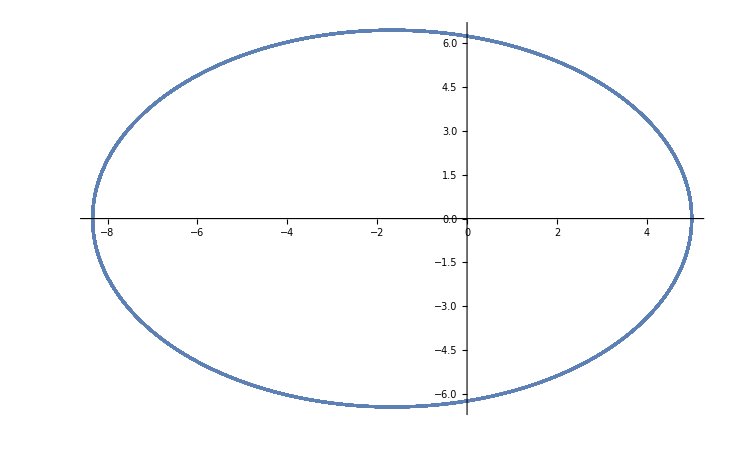

```mathematica
x0=5
y0=0
vx1={0};
vy1={.5}
h=10^-2
x1=N@{x0,x0+vx1[[1]]*h+h^2/2*-x0/((x0^2+y0^2)^(3/2))}
y1=N@{y0,y0+vy1[[1]]*h+h^2/2*-y0/((x0^2+y0^2)^(3/2))}
For[i=3,i<100000,i++,
AppendTo[x1,2x1[[i-1]]-x1[[i-2]]+h^2(-x1[[i-1]])/((x1[[i-1]]^2+y1[[i-1]]^2)^(3/2)) ];
AppendTo[y1,2y1[[i-1]]-y1[[i-2]]+h^2(-y1[[i-1]])/((x1[[i-1]]^2+y1[[i-1]]^2)^(3/2)) ];
];
ListPlot[Transpose[{x1,y1}]]
```

## Velocity Verlet

Najpierw obliczamy:
 v(t+Δt/2)= v(t)+Δt/2 A(y(t)) 
wykorzystując v(t+Δt/2), znajdujemy:  y(t+Δt)=y(t)+ v(t+Δt/2)Δt,
znając y(t+Δt) obliczamy A( y(t + Δt) ), a na sam koniec otrzymujemy prędkość:
v(t+Δt)= v(t+Δt/2)+Δt/2 A(y(t+Δt))

y(t+Δt)=y(t) + v(t)Δt+1/2 A(y(t))Δt^2
v(t+Δt)=v(t) + (A( y(t) )+A( y(t+Δt) ))/2 Δt 
Do obliczenia A( y( t + Δt ) )

## Metody explicit vs implicit (jawne vs uwikłane?)

### Euler: f’(x) = A(f, x)

explicit (forward): 
(f(x+h)-f(x))/h = A(f(x),x)
 f(x+h) = f(x) + A(f(x), x)h

implicit (backward formula): 
(f(x+h)-f(x))/h = A(f(x+h),x)
 f(x+h) = f(x) + A(f(x+h), x+h) h
żeby dostać f(x+h) musimy rozwiązać dodatkowe równanie! (które może być nieliniowe)

### Podsumowanie

Metody jawne są łatwiejsze do zaimplementowania i szybsze

Metody uwikłane wymagają rozwiązania dodatkowego równania/układu równań, ale są dokładniejsze

## Metody Runge-Kutty

### Wstęp: równanie y’ = f(y,t)

Powyższe równanie możemy od-całkować:
 y(t+h) = y(t) + ∫_t^(t+h) f(y(t),t)dt 
Przybliżmy tą całkę korzystając z metody trapezów:
y(t+h) = y(t) + h/2( f(y(t+h),t+h)+f(y(t),t) ) <- metoda uwikłana! Nie znamy y(t+h) do obliczenia f(y(t+h),t+h). 
Rozwiązanie: skorzystajmy z metody Eulera: y(t+h) ≈ Y(t) = y(t) + h f(y(t),t), co daje rezultat:
y(t+h) = y(t) + h/2( f(Y(t),t+h)+f(y(t),t) )

### Metoda Runge-Kutty czwartego rzędu:

Analogicznie do poprzedniego przykładu ale oparta na metodzie Simpsona:

y’ = (y,t)

y(t+h)=y(t)+h/6( Y_1+2 Y_2+2 Y_3+Y_4 )

Y_1= f(y(t),t)
Y_2= f(y(t) + h/2 Y_1,t+h/2)
Y_3= f(y(t) + h/2 Y_2,t+h/2)
Y_4= f(y(t) + hY_3,t+h)

## Euler vs RK2 vs RK4

Rozwiążemy równanie y'(t)= -y^2, y(1)=1 trzema poznanymi metodami

```mathematica
sol=DSolveValue[{y'[t]==-y[t]^2,y[1]==1},y,t]
```

Function[{t},1/t]

```mathematica
D[-y[t]^2,t]/.{y'[t]->-y[t]^2}
D[2 y[t]^3,t]/.{y'[t]->-y[t]^2}
D[-6 y[t]^4,t]/.{y'[t]->-y[t]^2}
```

2 y[t]^3

-6 y[t]^4

24 y[t]^5

1/100

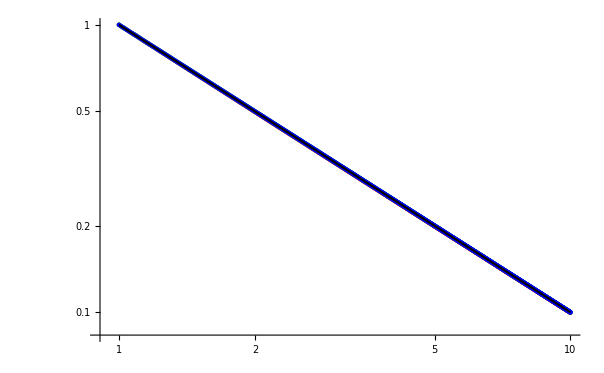

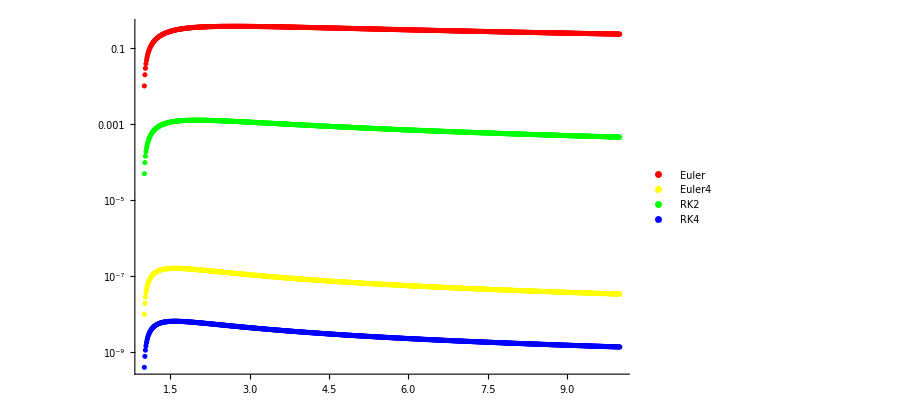

```mathematica
h=10^-2
time = Table[N@t,{t,1,10,h}];
xeuler={1};
xeuler4={1};
xRK2={1};
xRK4={1};
For[i=2,i<=Length[time],i++,
AppendTo[xeuler, N[xeuler[[i-1]]-xeuler[[i-1]]^2 h]];
AppendTo[xeuler4, N[xeuler4[[i-1]]-xeuler4[[i-1]]^2 h+h^2 xeuler4[[i-1]]^3-h^3 xeuler4[[i-1]]^4+h^4 xeuler4[[i-1]]^5]];
AppendTo[xRK2, N[xRK2[[i-1]]+(-xRK2[[i-1]]^2-(xRK2[[i-1]]-h xRK2[[i-1]]^2)^2)h/2]];
Y1=-xRK4[[i-1]]^2;
Y2=-(xRK4[[i-1]]+h/2 Y1)^2;
Y3=-(xRK4[[i-1]]+h/2 Y2)^2;
Y4=-(xRK4[[i-1]]+h Y3)^2;
AppendTo[xRK4, N[xRK4[[i-1]]+(Y1+2Y2+2Y3+Y4)h/6]];
]
Show[{
ListLogLogPlot[Transpose[{time,xeuler}],PlotStyle->Red,PlotRange->All],
ListLogLogPlot[Transpose[{time,xRK2}],PlotStyle->Green,PlotRange->All],
ListLogLogPlot[Transpose[{time,xRK4}],PlotStyle->Blue,PlotRange->All],
LogLogPlot[{sol[t]},{t,1,10},PlotStyle->Black,PlotRange->All]}]
Show[{
ListLogPlot[Transpose[{time,Abs[(xeuler-sol[time])/sol[time]]*100}],PlotStyle->Red,PlotRange->All,PlotLegends->{"Euler"}],

ListLogPlot[Transpose[{time,Abs[(xeuler4-sol[time])/sol[time]]*100}],PlotStyle->Yellow,PlotRange->All,PlotLegends->{"Euler4"}],

ListLogPlot[Transpose[{time,Abs[(xRK2-sol[time])/sol[time]]*100}],PlotStyle->Green,PlotRange->All,PlotLegends->{"RK2"}],
ListLogPlot[Transpose[{time,Abs[(xRK4-sol[time])/sol[time]]*100}],PlotStyle->Blue,PlotRange->All,PlotLegends->{"RK4"}]
},PlotRange->All]
```